```mathematica
GetSlope[p1_,p2_]:=
Module[{x1,x2,y1,y2,m,b},
{x1,y1}=p1;
{x2,y2}=p2;
m=(y2-y1)/(x2-x1);
m
]
```

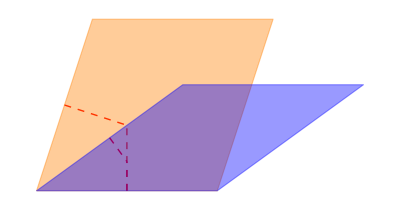

```mathematica
(*construct rhomb*)
(*a1={1,0};
a2S={Cos[36/180*Pi],Sin[36/180*Pi]};
a2F={Cos[72/180*Pi],Sin[72/180*Pi]};
a2S2={-Cos[36/180*Pi],Sin[36/180*Pi]};
a2F2={-Cos[72/180*Pi],Sin[72/180*Pi]};
TileF={EdgeForm[Thick],Orange,Opacity[0.4],Polygon[{{0,0},a2F,a1+a2F,a1}]};
TileS={EdgeForm[Thick],Blue,Opacity[0.4],Polygon[{{0,0},a2S,a1+a2S,a1}]};
TileF2={EdgeForm[Thick],Orange,Opacity[0.4],Polygon[{{0,0},a2F2,a1+a2F2,a1}]};
TileS2={EdgeForm[Thick],Blue,Opacity[0.4],Polygon[{{0,0},a2S2,a1+a2S2,a1}]};
Graphics[{TileF,TileS}]
Graphics[{TileF2,TileS2}]*)

a1={1,0};
a2S={Cos[36/180*Pi],Sin[36/180*Pi]};
a2F={Cos[72/180*Pi],Sin[72/180*Pi]};
TilePolyF={{0,0},a2F,a1+a2F,a1};
TilePolyS={{0,0},a2S,a1+a2S,a1};
VF1={a1/2,pF};
VF2={a2F/2,pF};
VS1={a1/2,pS};
VS2={a2S/2,pS};
TileF={EdgeForm[Thick],Orange,Opacity[0.4],Polygon[TilePolyF]};
TileS={EdgeForm[Thick],Blue,Opacity[0.4],Polygon[TilePolyS]};
mS=GetSlope[{0,0},a1+a2S];
pS={0.5,mS*0.5};
mF=GetSlope[{0,0},a1+a2F];
pF={0.5,mF*0.5};
VorF={{Dashed,Red,Thick,Line[VF1]},{Dashed,Red,Thick,Line[VF2]}};
VorS={{Dashed,Red,Thick,Line[VS1]},
{Dashed,Red,Thick,Line[VS2]}};
TileF=Join[VorF,TileF];
TileS=Join[VorS,TileS];
Graphics[{TileF,TileS}]
```

```mathematica
VF2end
```

{0.172746,0.601035}

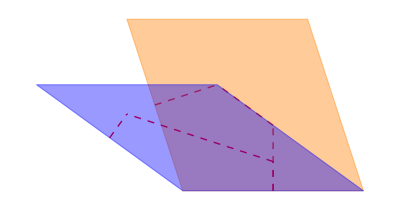

```mathematica
TilePolyFr=ReflectionMatrix[{1,0}].#+{1,0}&/@TilePolyF;
TilePolySr=ReflectionMatrix[{1,0}].#+{1,0}&/@TilePolyS;



VF1r=ReflectionMatrix[{1,0}].#+{1,0}&/@VF1;
VF2r=ReflectionMatrix[{1,0}].#+{1,0}&/@VF2;
VS1r=ReflectionMatrix[{1,0}].#+{1,0}&/@VS1;
VS2r=ReflectionMatrix[{1,0}].#+{1,0}&/@VS2;
TileF2={EdgeForm[Thick],Orange,Opacity[0.4],Polygon[TilePolyFr]};
TileS2={EdgeForm[Thick],Blue,Opacity[0.4],Polygon[TilePolySr]};
VF2end=TilePolyFr[[3]]-(VF1r[[2]]-TilePolyFr[[1]]);
VS2end=TilePolySr[[3]]-(VS1r[[2]]-TilePolySr[[1]]);
VorF2={{Dashed,Red,Thick,Line[VF1r]},{Dashed,Red,Thick,Line[{VF1r[[2]],VF2end}]},
{Dashed,Red,Thick,Line[{TilePolyFr[[3]]/2,VF2end}]}};
VorS2={{Dashed,Red,Thick,Line[VS1r]},{Dashed,Red,Thick,Line[{VS1r[[2]],VS2end}]},
{Dashed,Red,Thick,Line[{TilePolySr[[3]]/2,VS2end}]}};

TileF2=Join[VorF2,TileF2];
TileS2=Join[VorS2,TileS2];
Graphics[{TileF2,TileS2}]
```

```mathematica
CalcAngleDot[tileset_]:=
Module[{assoc,S1,S2,F1,F2},
assoc=<|S1->32,S2->180-32,F1->72,F2->180-72|>;
CurVal=0;
n=Length[tileset];
Do[
CurVal
,{i,Range[n]}]
]
```

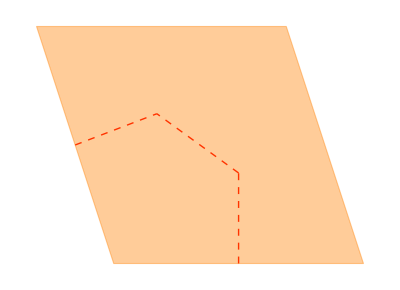

```mathematica
Graphics[TileF2]
```

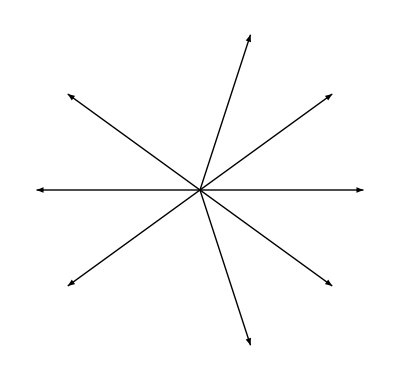

```mathematica
(*generate X*)
Xangles={36,36,72,36,36,72,36};
cur={1,0};
Xpts={cur};
Do[
AppendTo[Xpts,RotationMatrix[a Degree].cur];
cur=RotationMatrix[a Degree].cur;
,{a,Xangles}
]
Xpts=N[Xpts];
Graphics[Arrow[{{0,0},#}]&/@Xpts]
```

```mathematica
assoc=<|36->"S1",180-36->"S2",72->"F1",180-72->"F2"|>;
```

```mathematica
{72,36}/.assoc
```

{F1,S1}

```mathematica
Xsequence="S1 S1 S1 S1 F1 S1 S1 F1";
Ysequence="F1 S1 F1 S1 S1 S1 S1 S1";
```

```mathematica
Yangles={72,36,72,36,36,36,36};
cur={1,0};
Ypts={cur};
Do[
AppendTo[Ypts,RotationMatrix[a Degree].cur];
cur=RotationMatrix[a Degree].cur;
,{a,Yangles}
]
Ypts=N[Ypts];
Graphics[Arrow[{{0,0},#}]&/@Ypts]
```

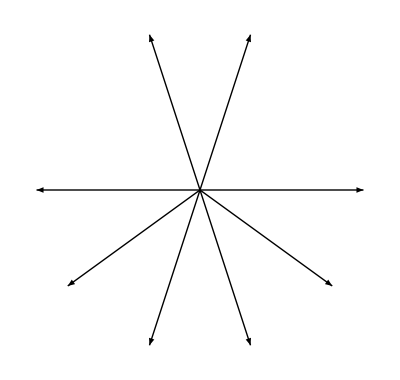

```mathematica
a=ArcCos[#.{1,0}]&/@Ypts;
Print[a];
n=Length[a];
b2=a[[Range[2,n]]]-a[[Range[1,n-1]]]
Sort[b2]
```

{0.,1.25664,1.88496,3.14159,2.51327,1.88496,1.25664,0.628319}

{1.25664,0.628319,1.25664,-0.628319,-0.628319,-0.628319,-0.628319}

{-0.628319,-0.628319,-0.628319,-0.628319,0.628319,1.25664,1.25664}

```mathematica
a=ArcCos[#.{1,0}]&/@Xpts;
Print[a];
n=Length[a];
b1=a[[Range[2,n]]]-a[[Range[1,n-1]]]
Sort[b1]
```

{0.,0.628319,1.25664,2.51327,3.14159,2.51327,1.25664,0.628319}

{0.628319,0.628319,1.25664,0.628319,-0.628319,-1.25664,-0.628319}

{-1.25664,-0.628319,-0.628319,0.628319,0.628319,0.628319,1.25664}

```mathematica
a=ArcCos[#.{1,0}]&/@(RotationMatrix[31Degree].#&/@Xpts);
Print[a];
n=Length[a];
b1=a[[Range[2,n]]]-a[[Range[1,n-1]]]
Total@Sort[b1]
```

{0.541052,1.16937,1.79769,3.05433,2.60054,1.97222,0.715585,0.0872665}

{0.628319,0.628319,1.25664,-0.453786,-0.628319,-1.25664,-0.628319}

-0.453786

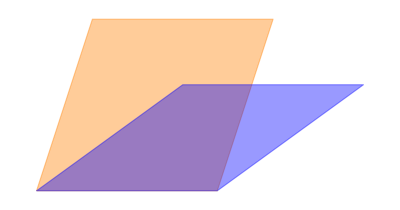

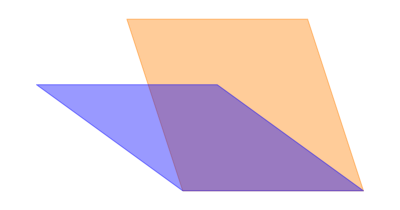

```mathematica
a1={1,0};
a2S={Cos[36/180*Pi],Sin[36/180*Pi]};
a2F={Cos[72/180*Pi],Sin[72/180*Pi]};
a2S2={-Cos[36/180*Pi],Sin[36/180*Pi]};
a2F2={-Cos[72/180*Pi],Sin[72/180*Pi]};
TileF={EdgeForm[Thick],Orange,Opacity[0.4],Polygon[{{0,0},a2F,a1+a2F,a1}]};
TileS={EdgeForm[Thick],Blue,Opacity[0.4],Polygon[{{0,0},a2S,a1+a2S,a1}]};
TileF2={EdgeForm[Thick],Orange,Opacity[0.4],Polygon[{{0,0},a2F2,a1+a2F2,a1}]};
TileS2={EdgeForm[Thick],Blue,Opacity[0.4],Polygon[{{0,0},a2S2,a1+a2S2,a1}]};
Graphics[{TileF,TileS}]
Graphics[{TileF2,TileS2}]
```

```mathematica
Labels={"D","Q","K","L","M","J","R","S","T","U","V","W","X","Y","Z","ST"};
```

```mathematica
(*
A:out skinny;
B:out fat;
C:in skinny;
D:in fat;
*)
```

```mathematica
Tiles={
"A B B",
"A D A",
"A D D D",
"B B C B",
"C B A D",
"B C D C B",
"A D C C D",
"D D D D D",
"C D D D D C",
"D C D C B C",
"D C C D D C C",
"D C D C C D C",
"C C D C C D C C",
"D C D C C C C C",
"C C C C D C C C C",
"C C C C C C C C C C"
};

Offsets={
-(180-36)/2,
0,
-(180-36)/2,
-(180-72)/2+90,
0,
0,
-(180-36)/2,
0,
0,
0,
-36,
-36,
0,
0,
0,
0
};

AssocAngle=<|"A"->180-36,"B"->180-72,"C"->36,"D"->72|>;
AssocTile=<|"A"->TileS2,"B"->TileF2,"C"->TileS,"D"->TileF|>;
```

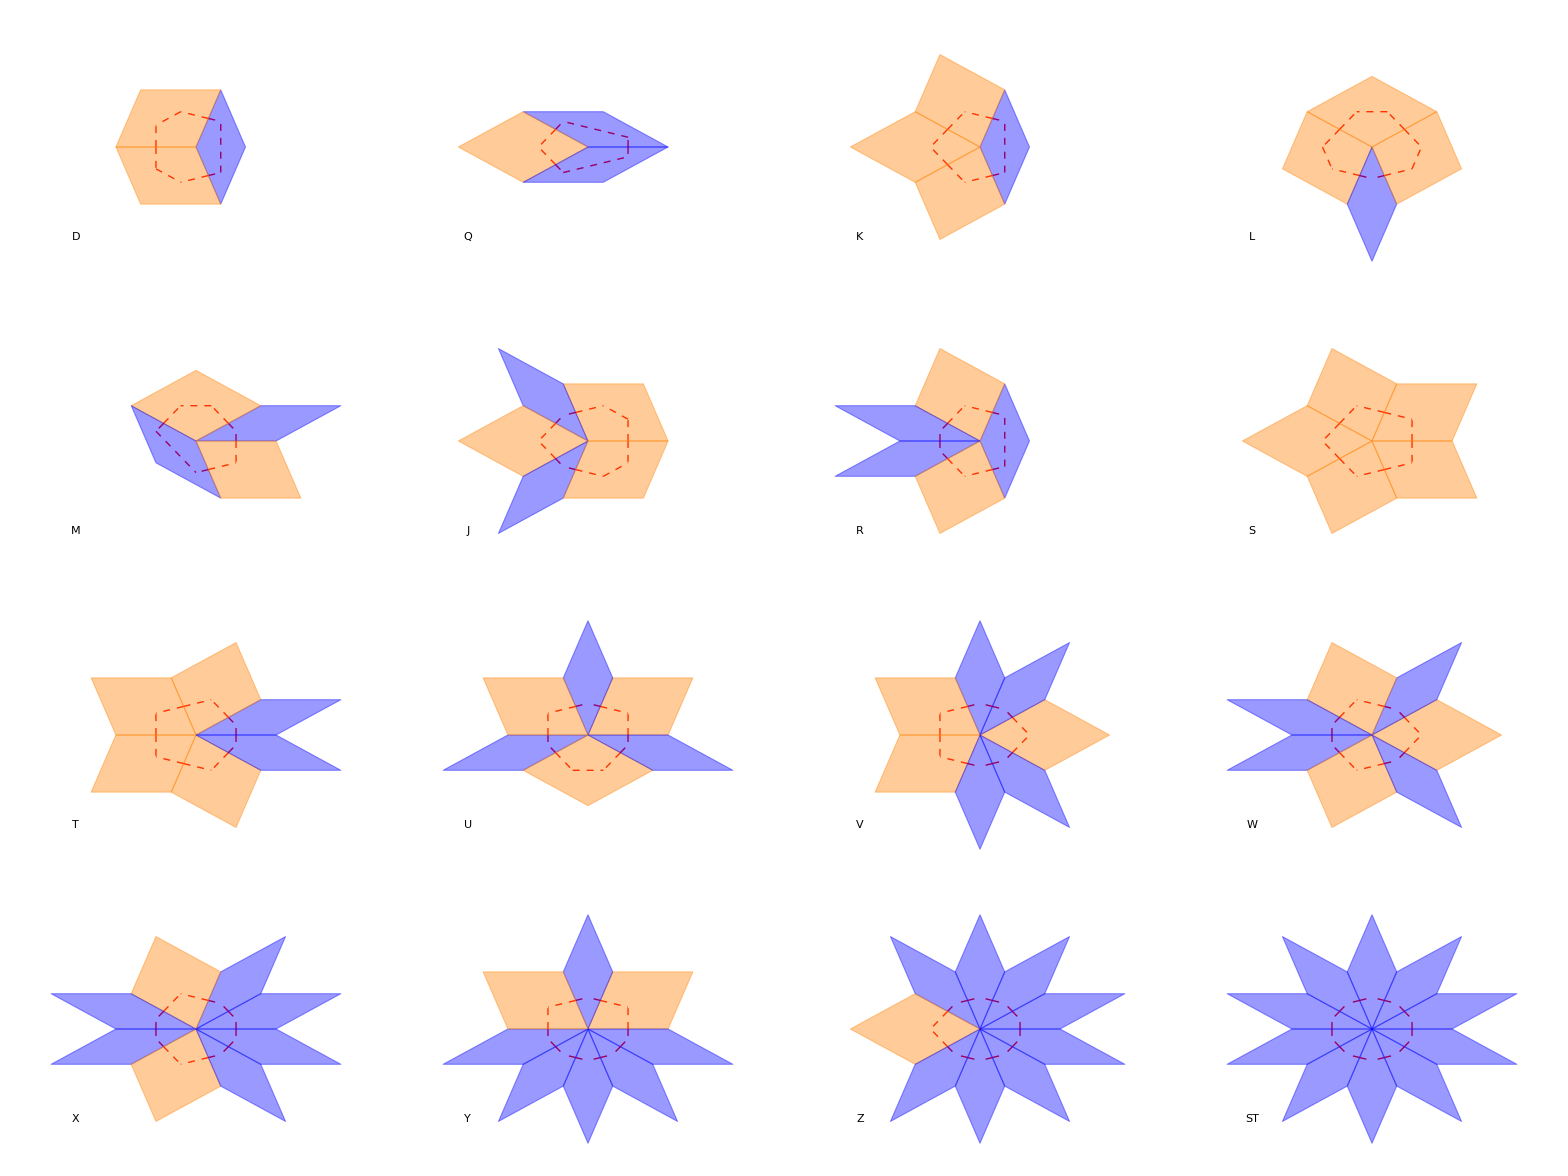

fig_vertices_4x4.pdf

```mathematica
r=1.8;
n=Length[Tiles];
Vertices={};
SetOptions[Text,BaseStyle->{FontFamily->"Times",FontSize->14}];
Do[
tile=Tiles[[j]];
offset=Offsets[[j]];
tile=StringSplit[tile];
m=Length[tile];
CurVertex={};
CurAngle=offset;
Do[
CurTile=tile[[m]];
AppendTo[CurVertex,Rotate[AssocTile[tile[[i]]],CurAngle Degree,{0,0}]];
CurAngle = CurAngle + AssocAngle[tile[[i]]];
,{i,Range[m]}
];
AppendTo[Vertices,Graphics[{CurVertex,Text[Labels[[j]],{-1.5,-1.5},BaseStyle->{FontFamily->"Times",FontSize->30}]},ImageSize->150,PlotRange->{{-2,2},{-2,2}},ImagePadding->{{Automatic,10},{Automatic,10}}]];
,{j,Range[n]}
]
Vertices=ArrayReshape[Vertices,{4,4}];
Grid[Vertices]
Export["fig_vertices_4x4.pdf",%,ImageResolution->600]
```



```mathematica
Graphics[Circle[{0,0},2]]
```

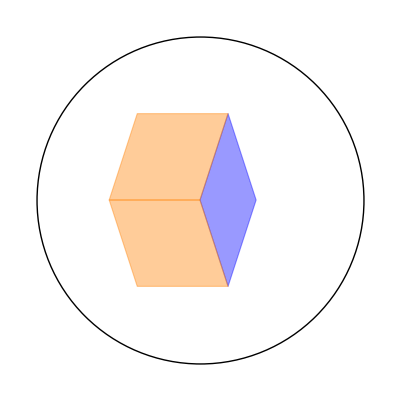

```mathematica
Vertices[[1,1]]
```